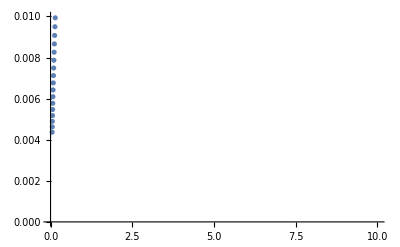

```mathematica
Te=0.4*1000*1.60217662*10^-19; (*Te=0.4 keV = in GENE*)
me=9.10938356*10^(-31);

vth=(3*Te/me)^(1/2);
imax=200; (*How many data points*)
jmax=100;
d=1000000^(1/imax);
w=1/6;(*Initial frequency*)
nu=1;
tempmax2=1;
Plottot=Range[tempmax2];
k0=Range[tempmax2];

k0[[1]]=0;
(*k0[[2]]=0.001;
k0[[3]]=0.1;
k0[[4]]=1;
k0[[5]]=10;
k0[[6]]=40;
k0[[7]]=-0.001;
k0[[8]]=-0.1;
k0[[9]]=-1;
k0[[10]]=-10;
k0[[11]]=-40;*)


For[temp=0,temp<tempmax2,temp++,
k=k0[[temp+1]];
Plot1=Range[imax];
For[i=0,i<imax, i++,
nu=d^i;
For[j=0,j<jmax ,j++,
w0=w;
B=NIntegrate[v^5(v^2/(2*vth^2)-3/2)Sin[x](Cos[x])^2/(
1-k*v*Cos[x]/w-I*nu*vth^3/(v^3*w)
)*Exp[-v^2/(2*vth^2)],{v,0,Infinity},{x,0,Pi}];

A=NIntegrate[v^5*Sin[x](Cos[x])^2/(
1-k*v*Cos[x]/w-I*nu*vth^3/(v^3*w)
)*Exp[-v^2/(2*vth^2)],{v,0,Infinity},{x,0,Pi}];
w=1+1.5*B/A;
dw=Abs[Abs[w]-Abs[w0]];
If[dw<Abs[w]*0.01, Break[],   ]
];
x=Abs[nu/(2*Pi*Re[w])];
y=Abs[Im[w]/(2*Pi*Re[w])];
Plot1[[i+1]]={x,y}
];

Plottot[[temp+1]]=Plot1
(*ListLogLinearPlot[Plot1]*)
];

ListPlot[
Plottot,
PlotRange->{{0,10},{0,0.01}}
]
```

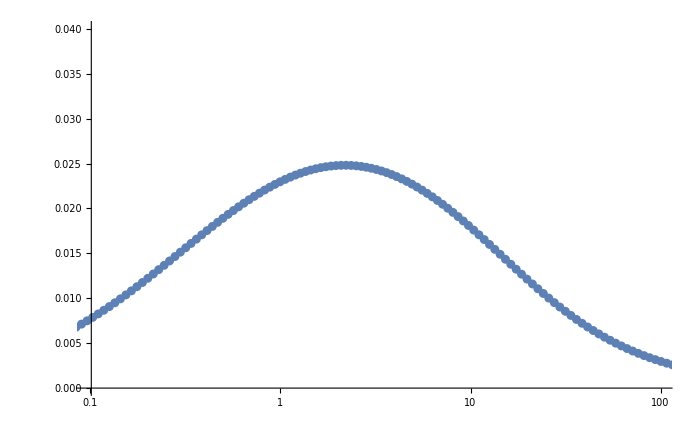

```mathematica
ListLogLinearPlot[
Plottot,
PlotRange->{{0,100},{0,0.04}}
]
```

```mathematica
Show[%200,AxesLabel->{ToExpression["\\frac{\\nu}{\\omega}",TeXForm,HoldForm],ToExpression["\\frac{\\nu}{\\omega}",TeXForm,HoldForm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

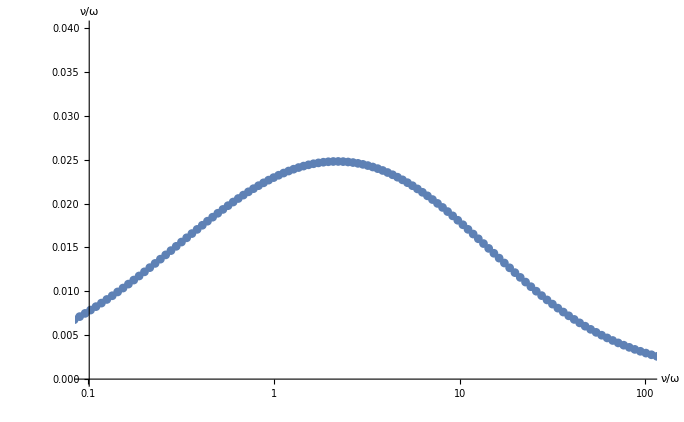

-Graphics-

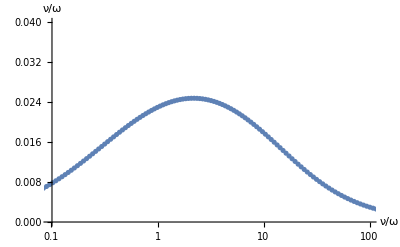

```mathematica
Show[%201,PlotLabel->None,LabelStyle->{20,GrayLevel[0]}]
```

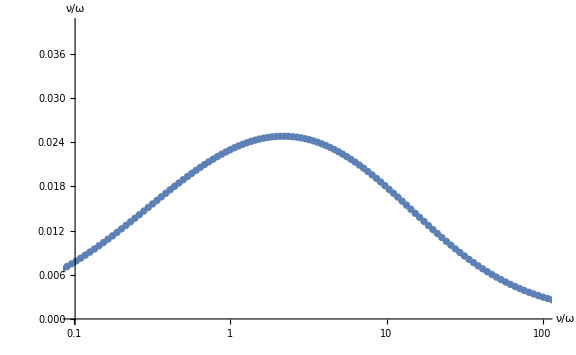

```mathematica
Show[%203,ImageSize->Large]
```

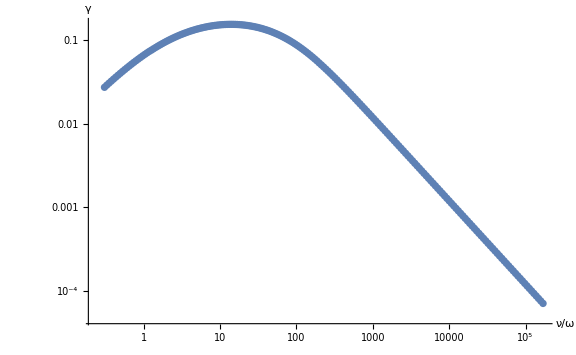

```mathematica
Show[%136,PlotLabel->None,LabelStyle->{20,GrayLevel[0]}]
```

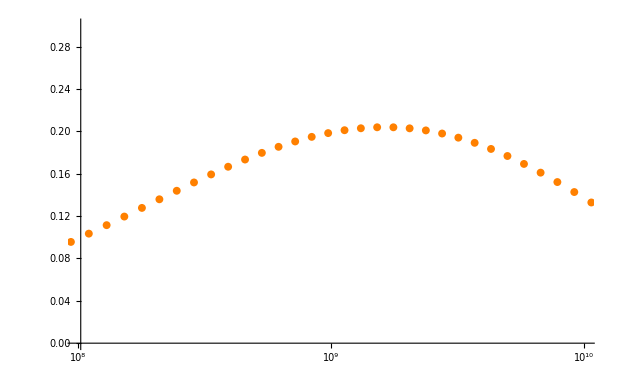

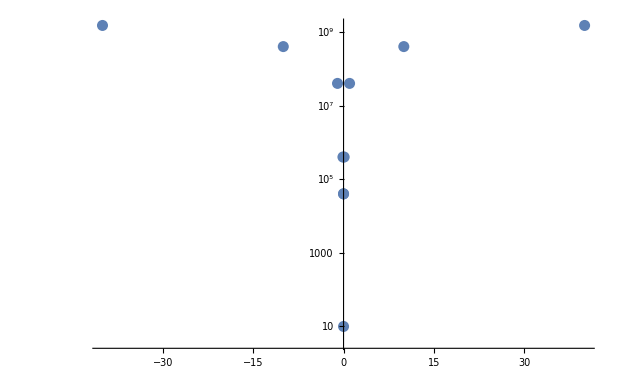

{{0,10},{0.001,40000},{0.1,400000},{1,40000000},{10,400000000},{40,1.5×10^9},{-0.001,40000},{-0.1,400000},{-1,40000000},{-10,400000000},{-40,1.5×10^9}}

```mathematica
plotk=Range[tempmax2];
(*k=n/R*(1-m/(n*q))*)
ListLogLinearPlot[Plottot[[6]],PlotStyle->{Orange}, 
PlotRange->{{10^8, 10^10},{0,0.3}}]
plotk[[1]]={k0[[1]],10};
plotk[[2]]={k0[[2]],4*10^4};
plotk[[3]]={k0[[3]],4*10^5};
plotk[[4]]={k0[[4]],4*10^7};
plotk[[5]]={k0[[5]],4*10^8};
plotk[[6]]={k0[[6]],1.5*10^9};
plotk[[7]]={k0[[7]],4*10^4};
plotk[[8]]={k0[[8]],4*10^5};
plotk[[9]]={k0[[9]],4*10^7};
plotk[[10]]={k0[[10]],4*10^8};
plotk[[11]]={k0[[11]],1.5*10^9};

ListLogPlot[plotk]
Print[plotk]
```

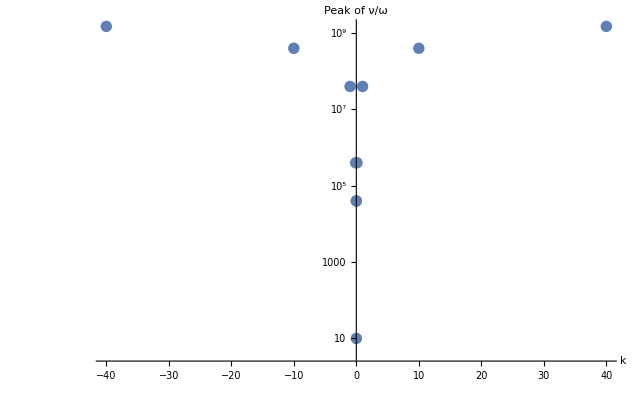

```mathematica
Show[%701,AxesLabel->{ToExpression["k",TeXForm,HoldForm],"Peak of"  ToExpression[ "\\frac{\\nu}{\\omega}",TeXForm,HoldForm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```